```mathematica
Quit[]
```

```mathematica
(* Package for plotting with LaTeX fonts *)
<<MaTeX`
LaunchKernels[];
$ProcessorCount
$KernelCount
```

32

32

## Fitting Function

### Genetic Algorithm

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]

PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)

PGA[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]

kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
Pkmax[h_,ωb_,ωm_,ns_,As_]:=(7080.944 As ⅇ^(-1.2303 ωb) h^2.081426)/(ns^1.49408 ωm^0.66927)
Rmax[h_,ωb_,ωm_,ns_]:=0.6461-0.0097 h^2+0.0307ns+7.1728ωb+0.0239/ωm
PGAmax[h_,ωb_,ωm_,ns_]:=(0.04682 ⅇ^(-8.611 ωb) ωm^1.0587)/(h^0.8998 ns^3.916)
DPGAmax[h_,ωb_,ωm_,ns_]:=-0.38598+0.005318h-0.00145 h^2+0.2277ns-0.086155 ns^2-1.86 ωb-28.6088 ωb^2+2.9997ωm-6.426 ωm^2
Bmax[h_,ωb_,ωm_,ns_]:=Rmax[h,ωb,ωm,ns]-1
Amax[h_,ωb_,ωm_,ns_,σmax_,λmax_]:=-(DPGAmax[h,ωb,ωm,ns]/PGAmax[h,ωb,ωm,ns])(1+Bmax[h,ωb,ωm,ns])-√(2/π)(λmax/σmax)Bmax[h,ωb,ωm,ns]
Pmax[k_,h_,ωb_,ωm_,ns_,σmax_,λmax_]:=1+(Amax[h,ωb,ωm,ns,σmax,λmax](k-kmax[h,ωb,ωm,ns])+Bmax[h,ωb,ωm,ns])ⅇ^(-1/2(k-kmax[h,ωb,ωm,ns])^2/σmax^2)(1+Erf[λmax*(k-kmax[h,ωb,ωm,ns])/(√2 σmax)])
```

### Cosmological Parameters

```mathematica
(* Formula from [2311.15865] *)
a0B=0.51172;
a1B=0.04593;
a2B=0.73983;
a3B=1.56738;
a4B=1.16846;
a5B=0.59348;
a6B=0.19994;
a7B=25.09218;
a8B=9.36909;
a9B=0.00011;
σ8[h_,Ωb_,Ωm_,ns_,As_]:=√As(a0B*Ωm+a1B*h+a2B*(Ωm-a3B*Ωb)(Log[a4B*Ωm]-a5B*ns)*(ns+a6B*h(a7B*Ωb-a8B*ns+Log[a9B*h])))
```

```mathematica
h=0.68;
ωb=0.022;
Ωb=ωb*h^-2;
ωc=0.12;
ωm=ωb+ωc;
Ωm=ωm*h^-2;
ns=0.96;
As=2.1;
```

```mathematica
(* Generar 1000 muestras alrededor del valor central *)
SeedRandom[12345];
mean={h,ωb,ωm,ns,As};
sigma={0.02,0.002,0.02,0.02,0.2}; 
distro=MultinormalDistribution[mean,DiagonalMatrix[sigma^2]];
Params=RandomVariate[distro,1000];
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GaussKronrodRule"},MaxRecursion->6,AccuracyGoal->6];
ti=AbsoluteTime[];
A0GA=ParallelTable[2*π^2(σ8[Params[[i,1]],Params[[i,2]]*Params[[i,1]]^2,Params[[i,3]]*Params[[i,1]]^2,Params[[i,4]],Params[[i,5]]]^2)/IntegralGA[i],{i,1,Length[Params]}];
tf=AbsoluteTime[];
Print["Time computing A_0: ",(tf-ti)*1000, " ms"]
```

Time computing A_0: 93.83 ms

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, max] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, max] *)
(* Fix Subscript[λ, max] = 0.4 *)
ti=AbsoluteTime[];
DDP=ParallelTable[D[D[PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σmax,λmax],k],k]/.k->kmax[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]],{i,1,Length[Params]}]//Simplify;
σDDP=ParallelTable[Solve[DDP[[i]]==DDPkclass[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]],σmax]//Quiet,{i,Length[Params]}];
(* Take the smallest one in absolute value *)
MinAbsKeepSign[pair_]:=First@MinimalBy[pair,Abs]
σGA=MinAbsKeepSign/@Table[{Re[σDDP[[i]][[1,1,2]]],Re[σDDP[[i]][[2,1,2]]]},{i,1,Length[Params]}];
tf=AbsoluteTime[];
Print["Time computing corrections: ",(tf-ti)*1000," ms"]
```

Time computing corrections: 526.026 ms

## Power Spectrum

### Smooth Transfer Function:

```mathematica
{TimeTnw,CalcTnw}=AbsoluteTiming[Tnw[k,#[[1]],#[[2]],#[[3]]]&/@Params[[All,1;;3]]];
Print["Time computing T_nw = ",TimeTnw*1000," ms"];
```

Time computing T_nw = 20.208 ms

```mathematica
CalcTnw[[1]]
```

1/((1+1126.57 k^1.483+1.31867×10^7 k^3.972+7.02249×10^8 k^6.097+2.74403×10^8 k^7.507)^(1/4))

```mathematica
Tnwexample[k_]:=(1/(1+1261.4546810624731 k^1.483+1.785165324588625*^7 k^3.972+1.1179067535690684*^9 k^6.097+4.864052688108795*^8 k^7.507)^(1/4))
```

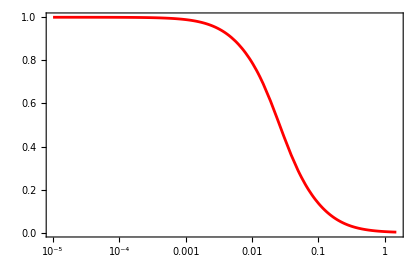

```mathematica
LogLinearPlot[Tnwexample[k],{k,10^-5,1.5},PlotStyle->{Directive[Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T_\\text{nw}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420]
```

### Wiggly Transfer Function:

```mathematica
{TimeTw,CalcTw}=AbsoluteTiming[Tw[k,#[[1]],#[[2]],#[[3]]]&/@Params[[All,1;;3]]];
Print["Time computing T_w = ",TimeTw*1000," ms"];
```

Time computing T_w = 31.718 ms

```mathematica
CalcTw[[1]]
```

1+(0.092583 ⅇ^(-8.91724 k^0.9914) Sin[(0.78991 (0.901515+95.9789 k))/((0.7349+0.00249761 (1/k)^1.19806)^0.739668)])/(1.03922+0.000253166 (1/k)^2.7345)

```mathematica
Twexample[k_]:=1+(0.09258296833002734 ⅇ^(-8.917241917471395 k^0.9914) Sin[(0.78991 (0.901515026740116+95.9789231446607 k))/((0.7349+0.0024976076752246685 (1/k)^1.19806)^0.739668)])/(1.03922+0.0002531662910860985 (1/k)^2.7345)
```

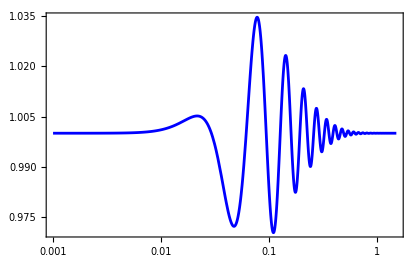

```mathematica
LogLinearPlot[Twexample[k],{k,10^-3,1.5},PlotRange->All,PlotStyle->{Directive[Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T_\\text{w}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420]
```

### Full Transfer Function:

```mathematica
{TimeTGA,CalcTGA}=AbsoluteTiming[TGA[k,#[[1]],#[[2]],#[[3]]]&/@Params[[All,1;;3]]];
Print["Tiempo total = ",TimeTGA*1000," ms"];
```

Tiempo total = 57.463 ms

```mathematica
CalcTGA[[1]]
```

((1-0.006249 ⅇ^(-254.483 (-0.199435+k)^2)) (1+(0.092583 ⅇ^(-8.91724 k^0.9914) Sin[(0.78991 (0.901515+95.9789 k))/((0.7349+0.00249761 (1/k)^1.19806)^0.739668)])/(1.03922+0.000253166 (1/k)^2.7345)))/((1+1126.57 k^1.483+1.31867×10^7 k^3.972+7.02249×10^8 k^6.097+2.74403×10^8 k^7.507)^(1/4))

```mathematica
TGAexample[k_]:=((1-0.006249 ⅇ^(-254.48306296067022 (-0.199435+k)^2)) (1+(0.09258296833002734 ⅇ^(-8.917241917471395 k^0.9914) Sin[(0.78991 (0.901515026740116+95.9789231446607 k))/((0.7349+0.0024976076752246685 (1/k)^1.19806)^0.739668)])/(1.03922+0.0002531662910860985 (1/k)^2.7345)))/(1+1126.5722405126955 k^1.483+1.3186740546376051*^7 k^3.972+7.022485259671928*^8 k^6.097+2.744027540198739*^8 k^7.507)^(1/4)
```

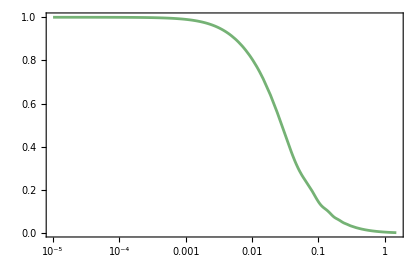

```mathematica
LogLinearPlot[TGAexample[k],{k,10^-5,1.5},PlotRange->All,PlotStyle->{Directive[RGBColor[0.1,0.5,0.1],Opacity[0.6]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T_\\text{GA}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420]
```

### Power Spectrum:

```mathematica
{TimePGA,CalcPGA}=AbsoluteTiming[MapThread[Function[{param,A0},Module[{h,ωb,ωm,ns,As},{h,ωb,ωm,ns,As}=param;
PGA[k,h,ωb,ωm,ns,A0]]],{Params,A0GA}]];

Print["Time computing P_GA = ",TimePGA*1000," ms"];
```

Time computing P_GA = 85.235 ms

```mathematica
CalcPGA[[1]]
```

(384401. (1-0.0038985 ⅇ^(-11.1111 (-1.1791+k)^2)) (1-0.006249 ⅇ^(-254.483 (-0.199435+k)^2))^2 (1-0.012538 ⅇ^(-17377. (-0.14376+k)^2)) (1+0.00837 ⅇ^(-612.685 (-0.081+k)^2)) k^0.949239 (1+(0.092583 ⅇ^(-8.91724 k^0.9914) Sin[(0.78991 (0.901515+95.9789 k))/((0.7349+0.00249761 (1/k)^1.19806)^0.739668)])/(1.03922+0.000253166 (1/k)^2.7345))^2)/(√(1+1126.57 k^1.483+1.31867×10^7 k^3.972+7.02249×10^8 k^6.097+2.74403×10^8 k^7.507))

```mathematica
PGAexample[k_]:=(384401.45009753504 (1-0.0038985 ⅇ^(-11.111111111111112 (-1.1791+k)^2)) (1-0.006249 ⅇ^(-254.48306296067022 (-0.199435+k)^2))^2 (1-0.012538 ⅇ^(-17376.980880246956 (-0.14376+k)^2)) (1+0.00837 ⅇ^(-612.6850308793256 (-0.081+k)^2)) k^0.9492391927381507 (1+(0.09258296833002734 ⅇ^(-8.917241917471395 k^0.9914) Sin[(0.78991 (0.901515026740116+95.9789231446607 k))/((0.7349+0.0024976076752246685 (1/k)^1.19806)^0.739668)])/(1.03922+0.0002531662910860985 (1/k)^2.7345))^2)/(√(1+1126.5722405126955 k^1.483+1.3186740546376051*^7 k^3.972+7.022485259671928*^8 k^6.097+2.744027540198739*^8 k^7.507))
```

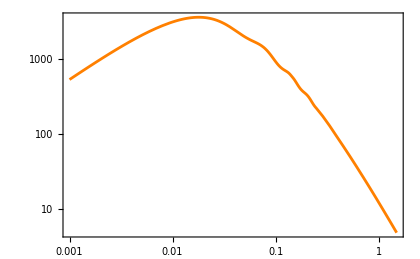

```mathematica
LogLogPlot[PGAexample[k],{k,10^-3,1.5},PlotRange->All,PlotStyle->{Directive[Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P_\\text{GA}(k) \\, [(\\text{Mpc}\\,h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420]
```

### Power Spectrum:

```mathematica
{TimePmax,CalcPmax}=AbsoluteTiming[MapThread[Function[{param,A0,σmax},Module[{h,ωb,ωm,ns,As},{h,ωb,ωm,ns,As}=param;
PGA[k,h,ωb,ωm,ns,A0]*Pmax[k,h,ωb,ωm,ns,σmax,λmax]]],{Params,A0GA,σGA}]];

Print["Time computing P_GA with corrections = ",TimePmax*1000," ms"];
```

Time computing P_GA with corrections = 127.2 ms

```mathematica
CalcPmax[[1]]
```

(384401. (1-0.0038985 ⅇ^(-11.1111 (-1.1791+k)^2)) (1-0.006249 ⅇ^(-254.483 (-0.199435+k)^2))^2 (1-0.012538 ⅇ^(-17377. (-0.14376+k)^2)) (1+0.00837 ⅇ^(-612.685 (-0.081+k)^2)) k^0.949239 (1+ⅇ^(-1.26602×10^9 (-0.0178082+k)^2) (-0.0177553+284.122 (-0.0178082+k)) (1+Erf[14232.5 (-0.0178082+k)])) (1+(0.092583 ⅇ^(-8.91724 k^0.9914) Sin[(0.78991 (0.901515+95.9789 k))/((0.7349+0.00249761 (1/k)^1.19806)^0.739668)])/(1.03922+0.000253166 (1/k)^2.7345))^2)/(√(1+1126.57 k^1.483+1.31867×10^7 k^3.972+7.02249×10^8 k^6.097+2.74403×10^8 k^7.507))

```mathematica
Pfullexample[k_]:=(384401.45009753504 (1-0.0038985 ⅇ^(-11.111111111111112 (-1.1791+k)^2)) (1-0.006249 ⅇ^(-254.48306296067022 (-0.199435+k)^2))^2 (1-0.012538 ⅇ^(-17376.980880246956 (-0.14376+k)^2)) (1+0.00837 ⅇ^(-612.6850308793256 (-0.081+k)^2)) k^0.9492391927381507 (1+ⅇ^(-1.2660205416822047*^9 (-0.017808187804937033+k)^2) (-0.01775525980945325+284.12188385429573 (-0.017808187804937033+k)) (1+Erf[14232.472963935423 (-0.017808187804937033+k)])) (1+(0.09258296833002734 ⅇ^(-8.917241917471395 k^0.9914) Sin[(0.78991 (0.901515026740116+95.9789231446607 k))/((0.7349+0.0024976076752246685 (1/k)^1.19806)^0.739668)])/(1.03922+0.0002531662910860985 (1/k)^2.7345))^2)/(√(1+1126.5722405126955 k^1.483+1.3186740546376051*^7 k^3.972+7.022485259671928*^8 k^6.097+2.744027540198739*^8 k^7.507))
```

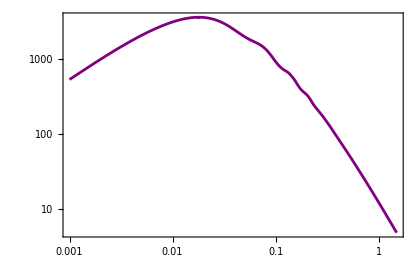

```mathematica
LogLogPlot[Pfullexample[k],{k,10^-3,1.5},PlotRange->All,PlotStyle->{Directive[Purple]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P_\\text{full}(k) \\, [(\\text{Mpc}\\,h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420]//Quiet
```